# stability analysis for local RK

```mathematica
ClearAll["Global`*"]
```

```mathematica
M=3;(*for now fixed,but could be changed in the future*)
Mp1=M+1;
size=(M+1)^2;
Nc=2*M+1;
ACCURACY=200;
ACCURACYPrint=30;
```

```mathematica
(*Gauss-Legendre nodes on reference interval[0,1] ANALYTICAL*)Points01=x/.Solve[LegendreP[M+1,x]==0,x];Points01=Re[(Points01+1)/2];
Points01=Sort[Points01,Less];
N[%]//MatrixForm
```

(0.0694318
0.330009
0.669991
0.930568)

```mathematica
(* Lagrange Polynomials through Gauss-Legendre nodes *)

PSI[p_, ξ_] := ∏_(k=1)^(M+1) If[k!=p,(ξ-Points01[[k]])/(Points01[[p]]-Points01[[k]]),1]
```

```mathematica
(*Derivative of Lagrange Polynomials*)
DPSI[p_,ξ_]:=D[PSI[p,x],x]/.x->ξ
DerivLagr2=Transpose[Table[Table[DPSI[i,Points01[[j]]],{j,1,Mp1}],{i,1,Mp1}]];
N[%]//MatrixForm
```

(-6.664 | 9.72031 | -4.21756 | 1.16126
-1.51512 | -0.768829 | 2.94134 | -0.657396
0.657396 | -2.94134 | 0.768829 | 1.51512
-1.16126 | 4.21756 | -9.72031 | 6.664)

```mathematica
(* Eigenvalues[DerivLagr2] *)
```

{0,0,0,0}

```mathematica
MatrixEvo[a_] := -a*DerivLagr2;
N[MatrixEvo[a]]//MatrixForm
```

(6.664 a | -9.72031 a | 4.21756 a | -1.16126 a
1.51512 a | 0.768829 a | -2.94134 a | 0.657396 a
-0.657396 a | 2.94134 a | -0.768829 a | -1.51512 a
1.16126 a | -4.21756 a | 9.72031 a | -6.664 a)

```mathematica
(* Eigenvalues[MatrixEvo[a]] *)
```

```mathematica
(* DimensionOfEigenspace =Table[Mp1 - MatrixRank[MatrixPower[MatrixEvo[a],p]],{p,1,Mp1}] *)
```

```mathematica
MatrixJ = ({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}});
```

```mathematica
Pchosen = IdentityMatrix[Mp1];
```

```mathematica
Pchosen[[All,3]] = MatrixEvo[a].(Pchosen[[All,4]]);
Pchosen[[All,2]] = MatrixEvo[a].(Pchosen[[All,3]]);
Pchosen[[All,1]] = MatrixEvo[a].(Pchosen[[All,2]]);
N[Pchosen]//MatrixForm
```

(-44.5232 a^3 | -12.7802 a^2 | -1.16126 a | 0.
-44.5232 a^3 | -1.17843 a^2 | 0.657396 a | 0.
-44.5232 a^3 | 13.9586 a^2 | -1.51512 a | 0.
-44.5232 a^3 | 25.5604 a^2 | -6.664 a | 1.)

```mathematica
PchosenInv = Inverse[Pchosen];
N[%]//MatrixForm
```

(-0.00314789/a^3 | -0.0151511/a^3 | -0.00416123/a^3 | 0.
-0.0411975/a^2 | 0.00671026/a^2 | 0.0344873/a^2 | 0.
-0.287045/a | 0.507051/a | -0.220005/a | 0.
-1. | 2.5329 | -2.5329 | 1.)

```mathematica
(*Test...*)
test=(Pchosen.MatrixJ.PchosenInv);
N[test]//MatrixForm
N[MatrixEvo[a]]//MatrixForm
%==%%
```

(6.664 a | -9.72031 a | 4.21756 a | -1.16126 a
1.51512 a | 0.768829 a | -2.94134 a | 0.657396 a
-0.657396 a | 2.94134 a | -0.768829 a | -1.51512 a
1.16126 a | -4.21756 a | 9.72031 a | -6.664 a)

(6.664 a | -9.72031 a | 4.21756 a | -1.16126 a
1.51512 a | 0.768829 a | -2.94134 a | 0.657396 a
-0.657396 a | 2.94134 a | -0.768829 a | -1.51512 a
1.16126 a | -4.21756 a | 9.72031 a | -6.664 a)

True

```mathematica
J1[a_] := MatrixEvo[a];
J2[a_] := MatrixEvo[a].MatrixEvo[a];
J3[a_] := MatrixEvo[a].MatrixEvo[a].MatrixEvo[a];;
J4[a_] := MatrixEvo[a].MatrixEvo[a].MatrixEvo[a];.MatrixEvo[a];;
```

```mathematica
R[a_]:=IdentityMatrix[Mp1]+h*J1[a] + h^2/2*J2[a] + h^3/6*J3[a] + h^4/24*J4[a]
N[R[a]]//MatrixForm
```

(1.+6.664 a h+12.7802 a^2 h^2+7.42054 a^3 h^3+1.85514 a^3 h^4 | -9.72031 a h-27.4732 a^2 h^2-18.7954 a^3 h^3-4.69886 a^3 h^4 | 4.21756 a h+21.0831 a^2 h^2+18.7954 a^3 h^3+4.69886 a^3 h^4 | -1.16126 a h-6.3901 a^2 h^2-7.42054 a^3 h^3-1.85514 a^3 h^4
1.51512 a h+6.97931 a^2 h^2+7.42054 a^3 h^3+1.85514 a^3 h^4 | 1.+0.768829 a h-12.7802 a^2 h^2-18.7954 a^3 h^3-4.69886 a^3 h^4 | -2.94134 a h+6.3901 a^2 h^2+18.7954 a^3 h^3+4.69886 a^3 h^4 | 0.657396 a h-0.589216 a^2 h^2-7.42054 a^3 h^3-1.85514 a^3 h^4
-0.657396 a h-0.589216 a^2 h^2+7.42054 a^3 h^3+1.85514 a^3 h^4 | 2.94134 a h+6.3901 a^2 h^2-18.7954 a^3 h^3-4.69886 a^3 h^4 | 1.-0.768829 a h-12.7802 a^2 h^2+18.7954 a^3 h^3+4.69886 a^3 h^4 | -1.51512 a h+6.97931 a^2 h^2-7.42054 a^3 h^3-1.85514 a^3 h^4
1.16126 a h-6.3901 a^2 h^2+7.42054 a^3 h^3+1.85514 a^3 h^4 | -4.21756 a h+21.0831 a^2 h^2-18.7954 a^3 h^3-4.69886 a^3 h^4 | 9.72031 a h-27.4732 a^2 h^2+18.7954 a^3 h^3+4.69886 a^3 h^4 | 1.-6.664 a h+12.7802 a^2 h^2-7.42054 a^3 h^3-1.85514 a^3 h^4)

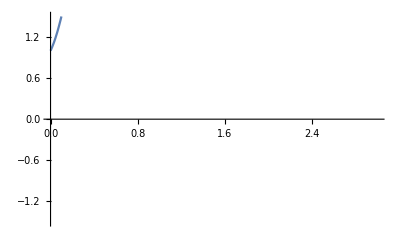

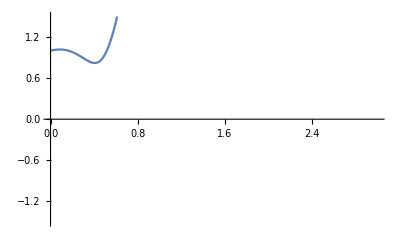

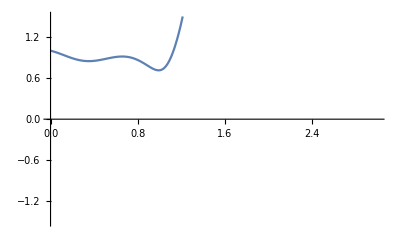

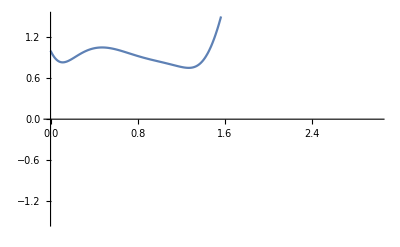

```mathematica
h = 0.5;
Plot[Norm[N[R[x][[1,All]]]],{x,0,3},PlotRange->1.5]
Plot[Norm[N[R[x][[2,All]]]],{x,0,3},PlotRange->1.5]
Plot[Norm[N[R[x][[3,All]]]],{x,0,3},PlotRange->1.5]
Plot[Norm[N[R[x][[4,All]]]],{x,0,3},PlotRange->1.5]
```

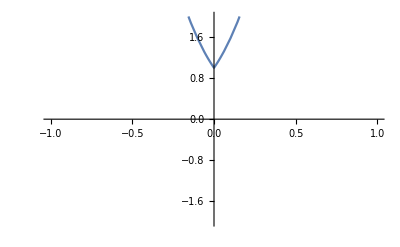

```mathematica
Plot[Norm[N[R[x]]],{x,-1,1},PlotRange->2]
```